```mathematica
MyFolderX=NotebookDirectory[]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/

```mathematica
(* Store filepath (string) of PersonData_ALL_N_354842_ALL.txt file in FilePathX *)
FilePathX=StringJoin[MyFolderX,"PersonData_ALL_N_354842_ALL.txt"]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/PersonData_ALL_N_354842_ALL.txt

```mathematica
(* Import Data > Store in the local variabe "Din" *)
Din=Import[FilePathX,"CSV",CharacterEncoding-> "UTF8","TextDelimiters"->"\""];
```

```mathematica
NDataALL = Length[Din]
```

354842

```mathematica
1.Time Period Between 1920s and 1930s  --Occupation Types in the United States [ During World War II ]
```

```mathematica
HeaderX={"Name","FullName","Gender","NationalityCountries","BirthDate","DeathDate","BirthPlace","DeathPlace","Occupation","Wives","Husbands"};

(* Choose from Dataset to obtain 1890s-1900s indivduals, and cleaning the data by getting rid of NotAvailable data, and rounding the year to decades.*)
```

```mathematica
DinFirst = Reap[For[i = 1, i<NDataALL, i++,
If[(ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 == 1930 || (ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 ==1940)) &&
(Din[[i]][[4]]== "UnitedStates")&&
(Din[[i]][[-3]]!= "NotAvailable"), Sow[Din[[i]]]
]]][[2]][[1]];
DinFirst[[1;;3]]
Length[DinFirst]
```

{{A. C. Cowlings,Allen G. Cowlings,Male,UnitedStates,1947-06-16,NotAvailable,SanFrancisco;California;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},{A.D. Whitfield,A.D. Whitfield,Male,UnitedStates,1943-09-02,NotAvailable,Rosebud;Texas;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},{A.D. Williams,A.D. Williams,Male,UnitedStates,1933-11-21,NotAvailable,LittleRock;Arkansas;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable}}

19327

```mathematica
2. Count Different Birth Years and Occupation Types from People Dataset
```

```mathematica
DBirthYearFirst = DinFirst
DBirthYearFirst= Reap[For[i = 1, i <= Length[DBirthYearFirst], i++,
Sow[ToExpression[StringDrop[DBirthYearFirst[[i]][[5]],-7]]*10]]][[2]][[1]];
```

{{A. C. Cowlings,Allen G. Cowlings,Male,UnitedStates,1947-06-16,NotAvailable,SanFrancisco;California;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},19325,{Verna Bloom,Verna Bloom,Female,UnitedStates,1938-08-07,2019-01-09,Lynn;Massachusetts;UnitedStates,BarHarbor;Maine;UnitedStates,actor,NotAvailable,JayCocks::g3p2n}}
 |  |  |  |

```mathematica
(*The Amount of in this dataset *)
Length[DBirthYearFirst]
DBirthYearFirst[[1;;10]]
```

19327

{1940,1940,1930,1930,1940,1940,1930,1940,1930,1940}

```mathematica
DOccupationsFirst= DinFirst
DOccupationsFirst= Reap[For[i = 1, i <= Length[DOccupationsFirst], i++,
Sow[DOccupationsFirst[[i]][[-3]]]]][[2]][[1]];
```

{{A. C. Cowlings,Allen G. Cowlings,Male,UnitedStates,1947-06-16,NotAvailable,SanFrancisco;California;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},19325,{Verna Bloom,Verna Bloom,Female,UnitedStates,1938-08-07,2019-01-09,Lynn;Massachusetts;UnitedStates,BarHarbor;Maine;UnitedStates,actor,NotAvailable,JayCocks::g3p2n}}
 |  |  |  |

```mathematica
(* Combine Year and Occupation data sets,
sepereate the occupations for when an indidual has more than one *)
```

```mathematica
DOC = Transpose[{DBirthYearFirst,DOccupationsFirst}];
DOC[[1;;2]]

SplitDOC = Reap[For[i = 1,i≤Length[DOC],i++,
s = StringSplit[DOC[[i,2]],";"];

For[j = 1,j≤ Length[s],j++,
Sow[{DOC[[i,1]],s[[j]]}]
]

]][[2]][[1]];
```

{{1940,football player},{1940,football player}}

```mathematica
(* Tally the data and get the repeated times in dataset for years and occupations)
```

```mathematica
YDOC = Tally[Flatten[SplitDOC[[All,1]]]];
TableForm[YDOC]
ODOC=Tally[Flatten[SplitDOC[[All,2]]]];
TableForm[ODOC]
```

1940 | 15042
1930 | 9504

football player | 2678
auto racer | 32
actor | 1886
economist | 80
playwright | 71
novelist | 264
writer | 726
publisher | 49
journalist | 315
activist | 198
captain | 3
musician | 1143
baseball player | 2113
producer | 108
singer | 495
dancer | 43
singer/songwriter | 150
social worker | 3
author | 710
judge | 561
academy award winner | 93
television actor | 157
businessperson | 1236
painter | 156
politician | 1761
songwriter | 218
columnist | 49
diplomat | 235
designer | 14
lawyer | 209
academy award nominee | 149
drummer | 54
military officer | 24
fashion designer | 16
guitarist | 130
radio personality | 57
visual artist | 6
artist | 289
university teacher | 41
philosopher | 36
religious | 87
basketball player | 817
architect | 39
historian | 148
professional wrestler | 4
film actor | 73
political activist | 3
land artist | 6
coach | 17
american football player | 20
physician | 25
editor | 105
teacher | 97
photographer | 131
criminal | 73
astronomer | 35
attorney | 153
journalist, presenter | 1
computer programmer | 29
conductor | 39
pianist | 69
mathematician | 96
entrepreneur | 57
athlete | 396
educator | 239
professor | 242
military | 230
anthropologist | 13
model | 97
poet | 192
swimmer | 3
sports commentator | 4
famous by association | 20
television producer | 43
film director | 194
screenwriter | 135
tv personality | 37
government | 205
radio talk show host | 1
commentator | 27
philanthropist | 51
composer | 161
association football player | 1
legislator | 27
director | 103
golfer | 189
football coach | 124
record producer | 97
game programmer | 1
game designer | 9
sports figure | 10
sportscaster | 11
astronaut | 148
news presenter | 2
cartoonist | 24
computer scientist | 36
consultant | 25
lobbyist | 13
scholar | 52
parliamentarian | 1
physicist | 69
administrator | 32
farmer | 22
essayist | 26
psychologist | 41
voice actor | 77
inventor | 33
musicologist | 5
political scientist | 10
sociologist | 13
spy | 5
comedian | 75
film producer | 81
bandleader | 22
sinologist | 2
pundit | 13
actor, television director, professor, playwright | 1
performer | 19
arranger | 40
sculptor | 55
chef | 10
filmmaker | 17
scientist | 68
officer | 39
drug trafficker | 3
bishop | 9
mafioso | 5
critic | 56
illustration | 3
illustrator | 26
graphic designer | 3
president | 28
investor | 13
poker player | 8
nurse | 8
singer, actor | 2
literary critic | 9
translator | 16
singer-songwriter | 14
stage actor | 28
doctor | 27
salesman | 4
stockbroker | 1
trade unionist | 3
record producer, film producer, television producer, politician, talent manager | 1
horse trainer | 2
biochemist | 10
beauty queen | 39
pathologist | 3
biographer | 1
vocalist | 34
aeronautical engineer | 3
organist | 5
game show host | 11
jockey | 12
presenter | 10
social activist | 3
broadcaster | 14
homemaker | 2
equestrian | 1
ecologist | 3
political adviser | 4
immunologist | 2
talk show host | 21
sports commentator, announcer, actor, voice actor | 1
fan | 3
music producer | 28
basketball coach | 29
motorcycle racer | 10
engineer | 66
news anchor | 7
musher | 2
basketball coach, coach | 1
labor leader | 8
archaeologist | 5
actor, comedian, voice actor, screenwriter | 1
baseball coach | 2
school superintendent | 1
mountaineer | 2
psychiatrist | 11
choreographer | 18
biologist | 19
businessman | 1
baseball manager | 2
representative | 16
tennis player | 15
aviator | 7
bassist | 11
banker | 14
astrophysicist | 11
television director | 22
geologist | 6
researcher | 8
botanist | 4
financier | 7
chairman | 1
songwriter, singer, singer-songwriter | 1
cardiologist | 1
commander | 5
chess master | 1
photojournalist | 10
television producer, screenwriter, television director, cinematographer | 1
public servant | 3
secretary | 1
correspondent | 8
master | 5
wrestler | 38
band manager | 1
political theorist | 2
film editor | 10
cinematographer | 10
camera operator | 1
sound artist | 2
impresario | 2
promoter | 4
film score composer | 7
head coach | 1
runner | 11
entertainer | 4
athletics competitor | 2
hockey player | 6
lawyer, businessperson, politician | 1
disc jockey | 13
animal trainer | 7
academic | 21
geneticist | 4
hitman | 1
magician | 10
blogger | 4
executive officer | 1
soldier | 5
unspecified | 6
scriptwriter | 1
federal judge | 3
radio/tv announcer | 1
real estate broker | 3
environmental science | 1
technician | 1
lichenologist | 1
chemist | 24
econometrician | 1
macroeconomist | 1
linguist | 8
tv anchor, journalist, presenter | 1
buseinessperson | 1
actor, voice actor | 3
tv anchor, tv journalist, journalist, actor, pilot, author | 1
professional boxer | 3
writer, gossip columnist, biographer, memoirist, journalist | 1
singer, actor, television producer | 1
cia operative | 1
film producer, entrepreneur, music executive | 1
hoaxer | 2
secret service agent | 1
bodyguard | 1
intelligence agent | 2
cattle rancher | 4
agent | 2
aristocrat | 1
environmental campaigner | 1
militant activist | 2
oceanographer | 2
pornographic actor | 18
drummer, musician | 1
humorist | 5
stunt performer | 5
martial artist | 4
military personnel | 10
ambassador | 2
assassin | 4
sportswriter | 2
gangster | 1
puppeteer | 6
adventurer | 2
business magnate | 1
restaurateur | 2
sailor | 3
volcanologist | 1
college president | 3
illusionist | 1
legal analyst | 1
associate professor | 1
lecturer | 11
seaman | 1
installation artist | 2
bassist, musician | 1
theologian | 2
miscellaneous crew | 3
pilot | 10
industrial designer | 3
jewelry designer | 1
violinist | 4
jurist | 4
professional soccer player | 1
singer, musician, guitarist | 1
singer, musician, singer-songwriter, actor, guitarist, pianist, film score composer | 1
dance educator | 1
journalist, presenter, author, actor, newscaster | 1
satirist | 1
animator | 3
boxer | 21
psychoanalyst | 2
volleyball player | 2
dentist | 3
neuroscientist | 5
daredevil | 2
boxing trainer | 1
luthier | 1
lyricist | 8
police commissioner | 1
theoretical physicist | 8
art historian | 1
first lady | 6
actor, psychotherapist | 1
psychotherapist | 5
actor, flight attendant | 1
student | 2
music pedagogue | 2
flautist | 1
autobiographer | 2
political aide | 1
non-fiction writer | 1
board member | 1
motivational speaker | 4
canadian football player | 5
orator | 2
strongman | 1
corrections officer | 1
tattoo artist | 1
boxing promoter | 2
singer-songwriter | 9
television producer, screenwriter, television director, actor | 1
electrical engineer | 6
paleontologist | 4
serial killer | 12
film distributor | 1
personal aide | 1
singer, actor, dancer, choreographer | 1
singer-songwriter, singer | 1
actor, film director, screenwriter | 1
programmer | 4
conservationist | 1
professional poker player | 1
newspaper publisher, urban planner, businessperson, real estate development | 1
politician, lawyer | 2
bowler | 2
interior designer | 1
test pilot | 3
actor, voice actor, film producer | 1
anesthesiologist | 2
university professor | 1
promoter, record producer, tour promoter, producer, film producer | 1
game show contestant | 1
film director, television director, film producer, theatre director | 1
cultural critic | 4
knife maker | 2
actor, basketball player | 1
actor, model | 1
set decorator | 3
singer, songwriter, actor | 2
catholic nun | 1
science writer | 1
tv anchor | 1
announcer | 4
sports commentator, announcer | 1
executive | 2
performance artist | 9
rapper | 1
humanitarian | 1
film director, television director, film producer | 1
keyboard player, jazz pianist, songwriter, record producer, musician, singer, composer, film score composer, music arranger | 1
public transit planner | 1
public transit supervisor | 1
electronics engineer | 1
radio announcer | 1
radio producer | 2
chess player | 2
software engineer | 2
business executive | 5
sports team owner | 5
fugitive | 1
statistician | 5
jazz musician | 7
film producer, television producer, author, actor, businessperson, record producer | 1
pharmacologist | 1
theatrical producer | 1
hacker | 3
prisoner | 1
spree killer | 1
fashion model | 3
graphic artist | 1
royalty | 2
senator | 2
women's advocate | 1
basketball player, basketball coach, athlete, coach | 1
photographer, film director, producer, writer, actor | 1
art dealer | 1
environmentalist | 2
television producer, screenwriter, film producer | 1
comic book artist | 3
truck driver | 1
production designer | 10
art director | 9
sports broadcaster | 1
computer engineer | 5
wrestler, actor | 1
coach, author, editor, tennis coach | 1
concert pianist | 2
costume designer | 2
social scientist | 1
civil engineer | 1
record producer, songwriter, film score composer | 2
feminist | 3
piano teacher | 1
neurobiologist | 1
investment analyst | 1
table tennis player | 1
umpire | 3
narrator | 1
scenographer | 2
human rights activist | 1
librarian | 3
law enforcement officer | 3
lawyer, judge | 2
magistrate | 1
actor, screenwriter | 2
gospel singer | 1
priest | 3
socialite | 6
environmental scientist | 1
film critic | 4
pitcher | 1
keyboardist | 3
manager | 1
emeritus | 1
memoirist | 1
screenwriter, television producer | 1
stand-up comedian | 1
forensic scientist | 2
skier | 2
criminologist | 1
opera singer | 3
rabbi | 1
children's writer | 2
logician | 1
music promoter | 4
war photographer | 1
lithographer | 2
epidemiologist | 1
music critic | 2
composer, radio personality, jazz pianist | 1
swimming coach | 1
murderer | 2
radio host | 1
stand-up comedian | 1
comedian, actor, musician, composer | 1
writer, actor, screenwriter | 1
bodybuilder | 3
singer, actor, voice actor | 1
real estate developer | 5
government official | 3
neurologist | 1
neuropsychiatrist | 1
millwright | 1
fitness guru | 2
clarinetist | 1
tennis coach | 2
construction worker | 1
saxophonist | 5
detective | 1
singer, musician, actor, songwriter, singer-songwriter | 1
microbiologist | 2
actor, singer | 2
ceramist | 1
lexicographer | 1
agriculturer | 4
medical scientist | 1
hedge fund manager | 1
entrepreneur, electrical engineer, engineer, businessperson, computer scientist | 1
cryptographer | 1
brigadier general | 1
surgeon | 7
music publisher | 1
revolutionary | 1
television presenter | 1
pharmacist | 1
veterinarian | 1
writer, actor, comedian, entertainer | 1
minister | 2
record producer, actor, film producer, voice actor, television producer, screenwriter, singer | 1
musician, songwriter, keyboard player | 1
reporter | 4
speaker | 3
advertising person | 1
businessperson, film producer, tv program creator | 1
cook | 1
sports announcer | 1
cyclist | 1
television personality | 6
venture capitalist | 1
announcer, commentator | 1
firefighter | 1
lawyer, jurist, referee, judge, soldier | 1
government officer | 1
mathematical physicist | 2
fashion model, actor | 1
theatre director | 3
retired | 1
literary agent | 1
spokesperson | 2
fitness professional | 1
chief operating officer | 1
clown | 1
professional wrestling booker | 1
landscape architect | 1
civil servant | 4
film scholar | 1
computer designer | 1
funeral director | 1
theater director | 2
actor, singer, disc jockey | 1
art critic | 1
disk jockey | 1
radio personality, disc jockey, actor | 1
investment banker | 2
aircraft pilot | 1
missionary | 1
clinician | 2
planetary geologist | 2
ethnographer | 1
music arranger | 1
trumpeter | 2
brett kavanaugh | 1
thief | 1
damage controlman | 1
police officer | 6
auto mechanic | 1
businessperson, lawyer | 1
american football player, american football coach, coach | 1
chief executive officer | 5
journalist, tv anchor | 1
ballet dancer, actor | 1
mathematicians | 1
counselor | 1
meteorologist | 1
comedian, actor, musician | 1
congressional staff | 1
community organizer | 1
artist, visual artist | 1
hairdresser | 1
patent inventor | 1
novelist, singer, actor | 1
urban planner | 1
skater | 1
nun | 1
airman | 1
judo expert | 1
ballet dancer | 1
artificial intelligence researcher | 1
fiddler | 1
ufologist | 3
printmaker | 4
theorist | 2
film producer, businessperson | 2
trader | 1
instructor | 1
housewife | 1
sound editor | 1
brigadier | 2
songwriter, organist, session musician | 1
nuclear scientist | 1
actress | 1
aerospace engineer | 2
aerospace engineering | 1
medical researcher | 4
percussionist | 1
gunsmith | 1
hotelier | 1
political economist | 1
film producer, entrepreneur, author | 1
public speaker | 3
comic creator | 1
recording engineer | 1
zoologist | 1
ornithologist | 1
entrepreneur, writer, businessperson | 1
actor, author, businessperson, activist | 1
actor, musician | 1
singer, songwriter, bandleader, entrepreneur | 1
lawyer, writer | 1
pastor | 3
security officer | 1
media executive | 1
police detective | 1
manufacturer | 1
endocrinologist | 1
chaplain | 1
technology evangelist | 1
imam | 1
gardener | 1
wood carver | 1
poster artist | 1
canoeist | 1
curator | 2
referee | 1
singer, composer, songwriter, singer-songwriter | 1
talent agent | 4
american football player, actor, teacher | 1
surfer | 1
racing driver | 1
record producer, engineer, audio engineer, musician, actor | 1
singer, musician, record producer, songwriter | 1
horse breeder | 1
mathematician, scientist, author, gambler, teacher | 1
computer scientist, film director, film producer | 1
world record holder | 1
cinematographer, film director, writer, artist, documentary filmmaker | 1
virologist | 1
actor, film producer, screenwriter, film director | 1
drummer, film score composer | 1
interior decorator | 2
businessperson, sports agent, lawyer | 1
session musician | 1
actor, screenwriter, film producer | 1
inventor, physicist | 1
vice president | 1
chiropractor | 1
music historian | 1
drug lord | 2
boss | 1
analyst | 2
advocate | 2
librettist | 2
pollster | 1
explorer | 2
casting director | 1
suspect | 1
theater founder | 1
general officer | 1
neurophysiologist | 1
computational biologist | 2
science fiction writer | 1
executive vice president | 1
drawer | 1
historian, writer, novelist, author | 1
martial arts instructor | 1
radio personality, actor, disc jockey | 1
documentarian | 1
film director, photographer | 1
craftsman | 1
law clerk | 1
solicitor | 1
television show host | 1
astrologer | 1
television writer | 1
héroe nacional (sin capa) | 1
cartographer | 1
topologist | 1
museum director | 2
televangelist | 2
evangelist, broadcaster, television producer | 1
actor, art collector | 1
biophysicist | 2
economist, professor | 1
country musician | 1
novelist, writer, author | 1
tv host | 2
comics writer | 1
journalist, politician, economist, businessperson, professor | 1
university president | 1
actor, teacher | 1
talent manager | 2
film producer, talent manager, businessperson, music executive, music publisher, record producer | 1
entrepreneur, businessperson | 1
make-up artist | 1
paranormal | 2
film director, television director, television producer, actor, screenwriter | 1
businessperson, entrepreneur | 1
zookeeper | 1
lacrosse coach | 1
nascar team owner | 1
evangelist | 1
preacher | 1
journalist, coach, film producer | 1
rancher | 1
master distiller | 1
television producer, television director, screenwriter, actor | 1
murder victim | 1
background artist | 1
concept artist | 1
background stylist | 1
businessperson, actor | 1
civil rights leader | 1
information theorist | 2
medical specialist | 1
boat designer | 1
futurist | 1
drag queen | 1
computational neuroscientist | 1
professional wrestling referee | 1
undertaker | 1
musician, singer-songwriter, songwriter, bassist | 1
optometrist | 1
labor advocate | 1
backgammon enthusiast | 1
rock climber | 1
chemical engineer | 1
television producer, screenwriter, film producer, film director | 1
sports historian | 1
businessperson, philanthropist | 1
bank teller, nurse | 1
disc jockey, radio personality, actor | 1
race car driver, american football player, coach | 1
businessperson, film producer, record producer | 1
basketball player, basketball coach | 1
lama | 1
entrepreneur, computer scientist | 1
naturalist | 1
journalist, sports commentator, actor, television producer, businessperson | 1
investor, author | 1
comedian, singer, singer-songwriter, actor, film score composer | 1
ski racer | 1
radio dj | 1
film/television producer | 1
musician, actor, drummer, singer | 1
writer, businessperson, coach, american football coach | 1
mobster | 1
professional golfer | 1
official | 1
racquetball player | 1
sheriff | 1
golfer, teacher | 1
boxing manager | 1

```mathematica
3) Define Bipartite matrix associating people with their interests - use a sorted interest-index
```

```mathematica
(* Only take the first 200 data from the split data, because the larger the dataset, the messier the graphs.
This way we can have a more clear overall analysis.*)
NewDOC = SplitDOC[[1;;200]];
NewDOC[[-1]]
```

{1930,anthropologist}

```mathematica
NewODOC = Tally[Flatten[NewDOC[[All,2]]]];
TableForm[NewODOC]
Length[NewODOC]
(* Below are the first 200 occupations and number of times they appear in 1890s - 1900s *)
```

football player | 27
auto racer | 1
actor | 17
economist | 1
playwright | 2
novelist | 3
writer | 5
publisher | 2
journalist | 3
activist | 3
captain | 1
musician | 8
baseball player | 16
producer | 1
singer | 4
dancer | 2
singer/songwriter | 2
social worker | 1
author | 4
judge | 1
academy award winner | 1
television actor | 1
businessperson | 13
painter | 2
politician | 14
songwriter | 2
columnist | 1
diplomat | 3
designer | 2
lawyer | 2
academy award nominee | 5
drummer | 3
military officer | 1
fashion designer | 1
guitarist | 2
radio personality | 2
visual artist | 1
artist | 5
university teacher | 1
philosopher | 1
religious | 1
basketball player | 3
architect | 2
historian | 2
professional wrestler | 1
film actor | 1
political activist | 1
land artist | 1
coach | 1
american football player | 1
physician | 1
editor | 1
teacher | 1
photographer | 1
criminal | 1
astronomer | 1
attorney | 1
journalist, presenter | 1
computer programmer | 1
conductor | 1
pianist | 1
mathematician | 1
entrepreneur | 1
athlete | 2
educator | 1
professor | 1
military | 1
anthropologist | 1

68

```mathematica
(* Create "dictionary" which maps a person/interest name to an index *)
Clear[MapYeari]
For[i=1,i≤Length[YDOC],i++,MapYeari[YDOC[[i,1]]]=i; ];
```

```mathematica
MapYeari[YDOC[[1,1]]]
MapYeari[YDOC[[-1,1]]]
```

1

2

```mathematica
Clear[MapOccupationj];
For[i=1,i≤Length[NewODOC],i++,MapOccupationj[NewODOC[[i]][[1]]]=i; ];
```

```mathematica
Length[NewODOC]
```

68

```mathematica
(* Calculate the bipartite association matrix *)
YearOccupationMatrix=Array[0&,{Length[YDOC],Length[NewODOC]}];
For[i=1,i≤Length[NewDOC],i++,
nInt=MapOccupationj[NewDOC[[i,2]]];
mInt=MapYeari[NewDOC[[i,1]]];
YearOccupationMatrix[[mInt]][[nInt]]=YearOccupationMatrix[[mInt]][[nInt]]+1;
];

MatrixForm[YearOccupationMatrix]
```

(15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1)

```mathematica
Show[Colorize[YearOccupationMatrix],ImageSize-> 400,AspectRatio-> 1]
```

-Graphics-

```mathematica
4) Define Year-Year and Occupation-Occupation association matrix using bipartite projection method
```

```mathematica
(* Year-Year association matrix *)
YearYearBipartiteProj=YearOccupationMatrix.Transpose[YearOccupationMatrix];
Length[YearYearBipartiteProj]
For[i=1,i≤ Length[YearYearBipartiteProj],i++, YearYearBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)
MatrixForm[YearYearBipartiteProj] (* Number of occupations are the same in these years*)
```

2

(0 | 423
423 | 0)

```mathematica
(* Occupation-Occupation association matrix *)
OccupationOccupationBipartiteProj=Transpose[YearOccupationMatrix].YearOccupationMatrix;
Length[OccupationOccupationBipartiteProj]
For[i=1,i≤ Length[OccupationOccupationBipartiteProj],i++, OccupationOccupationBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)

(* Display Matrix of first 20 occupaton to occupation *)
MatrixForm[OccupationOccupationBipartiteProj]
```

68

(0 | 12 | 228 | 15 | 24 | 39 | 69 | 24 | 42 | 42 | 15 | 117 | 228 | 15 | 51 | 27 | 27 | 15 | 54 | 15 | 15 | 15 | 183 | 24 | 198 | 30 | 15 | 36 | 30 | 24 | 66 | 42 | 12 | 12 | 30 | 27 | 15 | 66 | 15 | 15 | 12 | 42 | 30 | 27 | 15 | 15 | 15 | 12 | 15 | 15 | 15 | 12 | 12 | 12 | 15 | 12 | 15 | 15 | 15 | 15 | 15 | 15 | 12 | 27 | 12 | 12 | 15 | 12
12 | 0 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
228 | 9 | 0 | 8 | 18 | 26 | 42 | 18 | 25 | 25 | 8 | 65 | 132 | 8 | 35 | 17 | 17 | 8 | 34 | 8 | 8 | 8 | 108 | 18 | 116 | 16 | 8 | 27 | 16 | 18 | 43 | 25 | 9 | 9 | 16 | 17 | 8 | 43 | 8 | 8 | 9 | 25 | 16 | 17 | 8 | 8 | 8 | 9 | 8 | 8 | 8 | 9 | 9 | 9 | 8 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 17 | 9 | 9 | 8 | 9
15 | 0 | 8 | 0 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
24 | 2 | 18 | 0 | 0 | 4 | 4 | 4 | 2 | 2 | 0 | 2 | 8 | 0 | 6 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 8 | 4 | 8 | 0 | 0 | 6 | 0 | 4 | 6 | 2 | 2 | 2 | 0 | 2 | 0 | 6 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 2
39 | 2 | 26 | 1 | 4 | 0 | 7 | 4 | 4 | 4 | 1 | 9 | 20 | 1 | 7 | 3 | 3 | 1 | 6 | 1 | 1 | 1 | 17 | 4 | 18 | 2 | 1 | 6 | 2 | 4 | 8 | 4 | 2 | 2 | 2 | 3 | 1 | 8 | 1 | 1 | 2 | 4 | 2 | 3 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 2 | 1 | 2
69 | 2 | 42 | 3 | 4 | 7 | 0 | 4 | 8 | 8 | 3 | 23 | 44 | 3 | 9 | 5 | 5 | 3 | 10 | 3 | 3 | 3 | 35 | 4 | 38 | 6 | 3 | 6 | 6 | 4 | 12 | 8 | 2 | 2 | 6 | 5 | 3 | 12 | 3 | 3 | 2 | 8 | 6 | 5 | 3 | 3 | 3 | 2 | 3 | 3 | 3 | 2 | 2 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 3 | 3 | 2 | 5 | 2 | 2 | 3 | 2
24 | 2 | 18 | 0 | 4 | 4 | 4 | 0 | 2 | 2 | 0 | 2 | 8 | 0 | 6 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 8 | 4 | 8 | 0 | 0 | 6 | 0 | 4 | 6 | 2 | 2 | 2 | 0 | 2 | 0 | 6 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 2
42 | 1 | 25 | 2 | 2 | 4 | 8 | 2 | 0 | 5 | 2 | 15 | 28 | 2 | 5 | 3 | 3 | 2 | 6 | 2 | 2 | 2 | 22 | 2 | 24 | 4 | 2 | 3 | 4 | 2 | 7 | 5 | 1 | 1 | 4 | 3 | 2 | 7 | 2 | 2 | 1 | 5 | 4 | 3 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 3 | 1 | 1 | 2 | 1
42 | 1 | 25 | 2 | 2 | 4 | 8 | 2 | 5 | 0 | 2 | 15 | 28 | 2 | 5 | 3 | 3 | 2 | 6 | 2 | 2 | 2 | 22 | 2 | 24 | 4 | 2 | 3 | 4 | 2 | 7 | 5 | 1 | 1 | 4 | 3 | 2 | 7 | 2 | 2 | 1 | 5 | 4 | 3 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 3 | 1 | 1 | 2 | 1
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 0 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
117 | 1 | 65 | 7 | 2 | 9 | 23 | 2 | 15 | 15 | 7 | 0 | 88 | 7 | 10 | 8 | 8 | 7 | 16 | 7 | 7 | 7 | 67 | 2 | 74 | 14 | 7 | 3 | 14 | 2 | 17 | 15 | 1 | 1 | 14 | 8 | 7 | 17 | 7 | 7 | 1 | 15 | 14 | 8 | 7 | 7 | 7 | 1 | 7 | 7 | 7 | 1 | 1 | 1 | 7 | 1 | 7 | 7 | 7 | 7 | 7 | 7 | 1 | 8 | 1 | 1 | 7 | 1
228 | 4 | 132 | 12 | 8 | 20 | 44 | 8 | 28 | 28 | 12 | 88 | 0 | 12 | 24 | 16 | 16 | 12 | 32 | 12 | 12 | 12 | 124 | 8 | 136 | 24 | 12 | 12 | 24 | 8 | 36 | 28 | 4 | 4 | 24 | 16 | 12 | 36 | 12 | 12 | 4 | 28 | 24 | 16 | 12 | 12 | 12 | 4 | 12 | 12 | 12 | 4 | 4 | 4 | 12 | 4 | 12 | 12 | 12 | 12 | 12 | 12 | 4 | 16 | 4 | 4 | 12 | 4
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 0 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
51 | 3 | 35 | 1 | 6 | 7 | 9 | 6 | 5 | 5 | 1 | 10 | 24 | 1 | 0 | 4 | 4 | 1 | 8 | 1 | 1 | 1 | 21 | 6 | 22 | 2 | 1 | 9 | 2 | 6 | 11 | 5 | 3 | 3 | 2 | 4 | 1 | 11 | 1 | 1 | 3 | 5 | 2 | 4 | 1 | 1 | 1 | 3 | 1 | 1 | 1 | 3 | 3 | 3 | 1 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 3 | 4 | 3 | 3 | 1 | 3
27 | 1 | 17 | 1 | 2 | 3 | 5 | 2 | 3 | 3 | 1 | 8 | 16 | 1 | 4 | 0 | 2 | 1 | 4 | 1 | 1 | 1 | 13 | 2 | 14 | 2 | 1 | 3 | 2 | 2 | 5 | 3 | 1 | 1 | 2 | 2 | 1 | 5 | 1 | 1 | 1 | 3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1
27 | 1 | 17 | 1 | 2 | 3 | 5 | 2 | 3 | 3 | 1 | 8 | 16 | 1 | 4 | 2 | 0 | 1 | 4 | 1 | 1 | 1 | 13 | 2 | 14 | 2 | 1 | 3 | 2 | 2 | 5 | 3 | 1 | 1 | 2 | 2 | 1 | 5 | 1 | 1 | 1 | 3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
54 | 2 | 34 | 2 | 4 | 6 | 10 | 4 | 6 | 6 | 2 | 16 | 32 | 2 | 8 | 4 | 4 | 2 | 0 | 2 | 2 | 2 | 26 | 4 | 28 | 4 | 2 | 6 | 4 | 4 | 10 | 6 | 2 | 2 | 4 | 4 | 2 | 10 | 2 | 2 | 2 | 6 | 4 | 4 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 4 | 2 | 2 | 2 | 2
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 0 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 0 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 0 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
183 | 4 | 108 | 9 | 8 | 17 | 35 | 8 | 22 | 22 | 9 | 67 | 124 | 9 | 21 | 13 | 13 | 9 | 26 | 9 | 9 | 9 | 0 | 8 | 106 | 18 | 9 | 12 | 18 | 8 | 30 | 22 | 4 | 4 | 18 | 13 | 9 | 30 | 9 | 9 | 4 | 22 | 18 | 13 | 9 | 9 | 9 | 4 | 9 | 9 | 9 | 4 | 4 | 4 | 9 | 4 | 9 | 9 | 9 | 9 | 9 | 9 | 4 | 13 | 4 | 4 | 9 | 4
24 | 2 | 18 | 0 | 4 | 4 | 4 | 4 | 2 | 2 | 0 | 2 | 8 | 0 | 6 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 8 | 0 | 8 | 0 | 0 | 6 | 0 | 4 | 6 | 2 | 2 | 2 | 0 | 2 | 0 | 6 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 2
198 | 4 | 116 | 10 | 8 | 18 | 38 | 8 | 24 | 24 | 10 | 74 | 136 | 10 | 22 | 14 | 14 | 10 | 28 | 10 | 10 | 10 | 106 | 8 | 0 | 20 | 10 | 12 | 20 | 8 | 32 | 24 | 4 | 4 | 20 | 14 | 10 | 32 | 10 | 10 | 4 | 24 | 20 | 14 | 10 | 10 | 10 | 4 | 10 | 10 | 10 | 4 | 4 | 4 | 10 | 4 | 10 | 10 | 10 | 10 | 10 | 10 | 4 | 14 | 4 | 4 | 10 | 4
30 | 0 | 16 | 2 | 0 | 2 | 6 | 0 | 4 | 4 | 2 | 14 | 24 | 2 | 2 | 2 | 2 | 2 | 4 | 2 | 2 | 2 | 18 | 0 | 20 | 0 | 2 | 0 | 4 | 0 | 4 | 4 | 0 | 0 | 4 | 2 | 2 | 4 | 2 | 2 | 0 | 4 | 4 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
36 | 3 | 27 | 0 | 6 | 6 | 6 | 6 | 3 | 3 | 0 | 3 | 12 | 0 | 9 | 3 | 3 | 0 | 6 | 0 | 0 | 0 | 12 | 6 | 12 | 0 | 0 | 0 | 0 | 6 | 9 | 3 | 3 | 3 | 0 | 3 | 0 | 9 | 0 | 0 | 3 | 3 | 0 | 3 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 3 | 3 | 3 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 3 | 0 | 3
30 | 0 | 16 | 2 | 0 | 2 | 6 | 0 | 4 | 4 | 2 | 14 | 24 | 2 | 2 | 2 | 2 | 2 | 4 | 2 | 2 | 2 | 18 | 0 | 20 | 4 | 2 | 0 | 0 | 0 | 4 | 4 | 0 | 0 | 4 | 2 | 2 | 4 | 2 | 2 | 0 | 4 | 4 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 0
24 | 2 | 18 | 0 | 4 | 4 | 4 | 4 | 2 | 2 | 0 | 2 | 8 | 0 | 6 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 8 | 4 | 8 | 0 | 0 | 6 | 0 | 0 | 6 | 2 | 2 | 2 | 0 | 2 | 0 | 6 | 0 | 0 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 2
66 | 3 | 43 | 2 | 6 | 8 | 12 | 6 | 7 | 7 | 2 | 17 | 36 | 2 | 11 | 5 | 5 | 2 | 10 | 2 | 2 | 2 | 30 | 6 | 32 | 4 | 2 | 9 | 4 | 6 | 0 | 7 | 3 | 3 | 4 | 5 | 2 | 13 | 2 | 2 | 3 | 7 | 4 | 5 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 5 | 3 | 3 | 2 | 3
42 | 1 | 25 | 2 | 2 | 4 | 8 | 2 | 5 | 5 | 2 | 15 | 28 | 2 | 5 | 3 | 3 | 2 | 6 | 2 | 2 | 2 | 22 | 2 | 24 | 4 | 2 | 3 | 4 | 2 | 7 | 0 | 1 | 1 | 4 | 3 | 2 | 7 | 2 | 2 | 1 | 5 | 4 | 3 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 3 | 1 | 1 | 2 | 1
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 0 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 0 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
30 | 0 | 16 | 2 | 0 | 2 | 6 | 0 | 4 | 4 | 2 | 14 | 24 | 2 | 2 | 2 | 2 | 2 | 4 | 2 | 2 | 2 | 18 | 0 | 20 | 4 | 2 | 0 | 4 | 0 | 4 | 4 | 0 | 0 | 0 | 2 | 2 | 4 | 2 | 2 | 0 | 4 | 4 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 0
27 | 1 | 17 | 1 | 2 | 3 | 5 | 2 | 3 | 3 | 1 | 8 | 16 | 1 | 4 | 2 | 2 | 1 | 4 | 1 | 1 | 1 | 13 | 2 | 14 | 2 | 1 | 3 | 2 | 2 | 5 | 3 | 1 | 1 | 2 | 0 | 1 | 5 | 1 | 1 | 1 | 3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 0 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
66 | 3 | 43 | 2 | 6 | 8 | 12 | 6 | 7 | 7 | 2 | 17 | 36 | 2 | 11 | 5 | 5 | 2 | 10 | 2 | 2 | 2 | 30 | 6 | 32 | 4 | 2 | 9 | 4 | 6 | 13 | 7 | 3 | 3 | 4 | 5 | 2 | 0 | 2 | 2 | 3 | 7 | 4 | 5 | 2 | 2 | 2 | 3 | 2 | 2 | 2 | 3 | 3 | 3 | 2 | 3 | 2 | 2 | 2 | 2 | 2 | 2 | 3 | 5 | 3 | 3 | 2 | 3
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 0 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 0 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
42 | 1 | 25 | 2 | 2 | 4 | 8 | 2 | 5 | 5 | 2 | 15 | 28 | 2 | 5 | 3 | 3 | 2 | 6 | 2 | 2 | 2 | 22 | 2 | 24 | 4 | 2 | 3 | 4 | 2 | 7 | 5 | 1 | 1 | 4 | 3 | 2 | 7 | 2 | 2 | 1 | 0 | 4 | 3 | 2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 3 | 1 | 1 | 2 | 1
30 | 0 | 16 | 2 | 0 | 2 | 6 | 0 | 4 | 4 | 2 | 14 | 24 | 2 | 2 | 2 | 2 | 2 | 4 | 2 | 2 | 2 | 18 | 0 | 20 | 4 | 2 | 0 | 4 | 0 | 4 | 4 | 0 | 0 | 4 | 2 | 2 | 4 | 2 | 2 | 0 | 4 | 0 | 2 | 2 | 2 | 2 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 2 | 0
27 | 1 | 17 | 1 | 2 | 3 | 5 | 2 | 3 | 3 | 1 | 8 | 16 | 1 | 4 | 2 | 2 | 1 | 4 | 1 | 1 | 1 | 13 | 2 | 14 | 2 | 1 | 3 | 2 | 2 | 5 | 3 | 1 | 1 | 2 | 2 | 1 | 5 | 1 | 1 | 1 | 3 | 2 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1
27 | 1 | 17 | 1 | 2 | 3 | 5 | 2 | 3 | 3 | 1 | 8 | 16 | 1 | 4 | 2 | 2 | 1 | 4 | 1 | 1 | 1 | 13 | 2 | 14 | 2 | 1 | 3 | 2 | 2 | 5 | 3 | 1 | 1 | 2 | 2 | 1 | 5 | 1 | 1 | 1 | 3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
15 | 0 | 8 | 1 | 0 | 1 | 3 | 0 | 2 | 2 | 1 | 7 | 12 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 9 | 0 | 10 | 2 | 1 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 2 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
12 | 1 | 9 | 0 | 2 | 2 | 2 | 2 | 1 | 1 | 0 | 1 | 4 | 0 | 3 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 4 | 2 | 4 | 0 | 0 | 3 | 0 | 2 | 3 | 1 | 1 | 1 | 0 | 1 | 0 | 3 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0)

```mathematica
(* Degree Distribution *)
DegreeX=Total[Sign[#]]&/@OccupationOccupationBipartiteProj
```

{67,38,67,49,38,67,67,38,67,67,49,67,67,49,67,67,67,49,67,49,49,49,67,38,67,49,49,38,49,38,67,67,38,38,49,67,49,67,49,49,38,67,49,67,49,49,49,38,49,49,49,38,38,38,49,38,49,49,49,49,49,49,38,67,38,38,49,38}

```mathematica
5) WeightedAdjacencyGraph[ ]
```

```mathematica
mat=Replace[OccupationOccupationBipartiteProj,0->Infinity,{2}]; (*  0s represented by infinity in WeightedAdjacencyGraph[ ] *)
OName=NewODOC[[All,1]];

(* Set Labels : The "keys" for each node will be the name stored in OName *)
NameFontSizeX=20;
NodeColorX=Black;
LabelsetBlack=Table[OName[[i]]->Placed[ Style[OName[[i]],FontFamily->"Helvetica",NameFontSizeX,NodeColorX],Center],{i,Length[OName]}]
```

{football player→Placed[football player,Center],auto racer→Placed[auto racer,Center],actor→Placed[actor,Center],economist→Placed[economist,Center],playwright→Placed[playwright,Center],novelist→Placed[novelist,Center],writer→Placed[writer,Center],publisher→Placed[publisher,Center],journalist→Placed[journalist,Center],activist→Placed[activist,Center],captain→Placed[captain,Center],musician→Placed[musician,Center],baseball player→Placed[baseball player,Center],producer→Placed[producer,Center],singer→Placed[singer,Center],dancer→Placed[dancer,Center],singer/songwriter→Placed[singer/songwriter,Center],social worker→Placed[social worker,Center],author→Placed[author,Center],judge→Placed[judge,Center],academy award winner→Placed[academy award winner,Center],television actor→Placed[television actor,Center],businessperson→Placed[businessperson,Center],painter→Placed[painter,Center],politician→Placed[politician,Center],songwriter→Placed[songwriter,Center],columnist→Placed[columnist,Center],diplomat→Placed[diplomat,Center],designer→Placed[designer,Center],lawyer→Placed[lawyer,Center],academy award nominee→Placed[academy award nominee,Center],drummer→Placed[drummer,Center],military officer→Placed[military officer,Center],fashion designer→Placed[fashion designer,Center],guitarist→Placed[guitarist,Center],radio personality→Placed[radio personality,Center],visual artist→Placed[visual artist,Center],artist→Placed[artist,Center],university teacher→Placed[university teacher,Center],philosopher→Placed[philosopher,Center],religious→Placed[religious,Center],basketball player→Placed[basketball player,Center],architect→Placed[architect,Center],historian→Placed[historian,Center],professional wrestler→Placed[professional wrestler,Center],film actor→Placed[film actor,Center],political activist→Placed[political activist,Center],land artist→Placed[land artist,Center],coach→Placed[coach,Center],american football player→Placed[american football player,Center],physician→Placed[physician,Center],editor→Placed[editor,Center],teacher→Placed[teacher,Center],photographer→Placed[photographer,Center],criminal→Placed[criminal,Center],astronomer→Placed[astronomer,Center],attorney→Placed[attorney,Center],journalist, presenter→Placed[journalist, presenter,Center],computer programmer→Placed[computer programmer,Center],conductor→Placed[conductor,Center],pianist→Placed[pianist,Center],mathematician→Placed[mathematician,Center],entrepreneur→Placed[entrepreneur,Center],athlete→Placed[athlete,Center],educator→Placed[educator,Center],professor→Placed[professor,Center],military→Placed[military,Center],anthropologist→Placed[anthropologist,Center]}

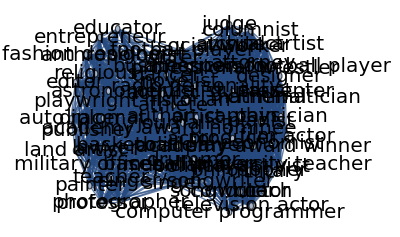

```mathematica
(* Plot Network - an ugly mess *)
g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack]
```

```mathematica
Clustering Coefficients - to what degree are neighbors connected?
```

```mathematica
(* Global - Network-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)
N[GlobalClusteringCoefficient[g]]
```

0.882368

```mathematica
(* Local - Node-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)LClusteringCoeffX=N[LocalClusteringCoefficient[g]]
Mean[LClusteringCoeffX]
N[MeanClusteringCoefficient[g]] (* Gives same result as above *)
```

{0.763908,1.,0.763908,1.,1.,0.763908,0.763908,1.,0.763908,0.763908,1.,0.763908,0.763908,1.,0.763908,0.763908,0.763908,1.,0.763908,1.,1.,1.,0.763908,1.,0.763908,1.,1.,1.,1.,1.,0.763908,0.763908,1.,1.,1.,0.763908,1.,0.763908,1.,1.,1.,0.763908,1.,0.763908,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.763908,1.,1.,1.,1.}

0.927089

0.927089

```mathematica
Length[LClusteringCoeffX]
```

68

```mathematica
Length[OName]
```

68

```mathematica
Sort[Thread[Rule[OName,LClusteringCoeffX]],#1[[2]]>#2[[2]]&]
```

{anthropologist→1.,military→1.,professor→1.,educator→1.,entrepreneur→1.,mathematician→1.,pianist→1.,conductor→1.,computer programmer→1.,journalist, presenter→1.,attorney→1.,astronomer→1.,criminal→1.,photographer→1.,teacher→1.,editor→1.,physician→1.,american football player→1.,coach→1.,land artist→1.,political activist→1.,film actor→1.,professional wrestler→1.,architect→1.,religious→1.,philosopher→1.,university teacher→1.,visual artist→1.,guitarist→1.,fashion designer→1.,military officer→1.,lawyer→1.,designer→1.,diplomat→1.,columnist→1.,songwriter→1.,painter→1.,television actor→1.,academy award winner→1.,judge→1.,social worker→1.,producer→1.,captain→1.,publisher→1.,playwright→1.,economist→1.,auto racer→1.,athlete→0.763908,historian→0.763908,basketball player→0.763908,artist→0.763908,radio personality→0.763908,drummer→0.763908,academy award nominee→0.763908,politician→0.763908,businessperson→0.763908,author→0.763908,singer/songwriter→0.763908,dancer→0.763908,singer→0.763908,baseball player→0.763908,musician→0.763908,activist→0.763908,journalist→0.763908,writer→0.763908,novelist→0.763908,actor→0.763908,football player→0.763908}

{{67,0.763908},{38,1.},{67,0.763908},{49,1.},{38,1.},{67,0.763908},{67,0.763908},{38,1.},{67,0.763908},{67,0.763908},{49,1.},{67,0.763908},{67,0.763908},{49,1.},{67,0.763908},{67,0.763908},{67,0.763908},{49,1.},{67,0.763908},{49,1.},{49,1.},{49,1.},{67,0.763908},{38,1.},{67,0.763908},{49,1.},{49,1.},{38,1.},{49,1.},{38,1.},{67,0.763908},{67,0.763908},{38,1.},{38,1.},{49,1.},{67,0.763908},{49,1.},{67,0.763908},{49,1.},{49,1.},{38,1.},{67,0.763908},{49,1.},{67,0.763908},{49,1.},{49,1.},{49,1.},{38,1.},{49,1.},{49,1.},{49,1.},{38,1.},{38,1.},{38,1.},{49,1.},{38,1.},{49,1.},{49,1.},{49,1.},{49,1.},{49,1.},{49,1.},{38,1.},{67,0.763908},{38,1.},{38,1.},{49,1.},{38,1.}}

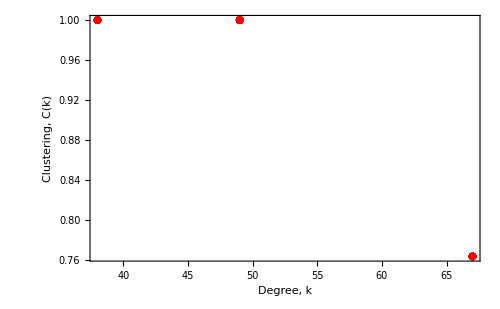

```mathematica
DegreeClusteringX=Thread[{DegreeX,LClusteringCoeffX}]

ListPlot[DegreeClusteringX,
PlotRange-> All,
PlotStyle->Directive[Red,10],
LabelStyle -> Directive[Black,FontSize->20,FontFamily-> "Helvetica"],
Frame->True,
ImageSize->{500,Automatic},
FrameLabel->{"Degree, k","Clustering, C(k)"},
ImageSize->500]
```

```mathematica
Improve network visualization layout
```

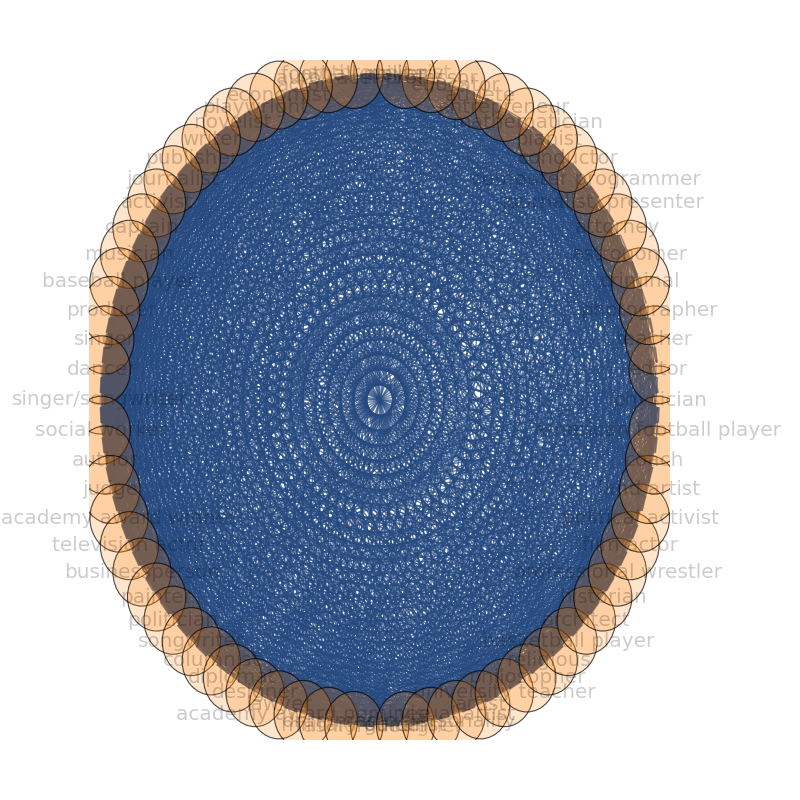

```mathematica
Circlesize=0.05;
r=Array[Circlesize&,Length[OName]]; (* Circle radius list *)

g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack,VertexSize->Scaled[.10],VertexStyle->Directive[Orange,Opacity[.2]],GraphLayout->{"CircularEmbedding"} ,ImageSize->800]
```

```mathematica
6) Modify the link color and thickness
```

```mathematica
(* AbsoluteOptions[ ]: gives the absolute settings of options specified in an expression such as a graphics object. *)
gEdWe=AbsoluteOptions[g,EdgeWeight][[All,2]][[1]]  (* Get list of edge weights associated with each edge *)
Max[gEdWe]
```

{12,228,15,24,39,69,24,42,42,15,117,228,15,51,27,27,15,54,15,15,15,183,24,198,30,15,36,30,24,66,42,12,12,30,27,15,66,15,15,12,42,30,27,15,15,15,12,15,15,15,12,12,12,15,12,15,15,15,15,15,15,12,27,12,12,15,12,9,2,2,2,2,1,1,1,4,3,1,1,2,4,2,4,3,2,3,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,8,18,26,42,18,25,25,8,65,132,8,35,17,17,8,34,8,8,8,108,18,116,16,8,27,16,18,43,25,9,9,16,17,8,43,8,8,9,25,16,17,8,8,8,9,8,8,8,9,9,9,8,9,8,8,8,8,8,8,9,17,9,9,8,9,1,3,2,2,1,7,12,1,1,1,1,1,2,1,1,1,9,10,2,1,2,2,2,2,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,4,4,2,2,2,8,6,2,2,4,8,4,8,6,4,6,2,2,2,2,6,2,2,2,2,2,2,2,2,2,2,2,2,2,7,4,4,4,1,9,20,1,7,3,3,1,6,1,1,1,17,4,18,2,1,6,2,4,8,4,2,2,2,3,1,8,1,1,2,4,2,3,1,1,1,2,1,1,1,2,2,2,1,2,1,1,1,1,1,1,2,3,2,2,1,2,4,8,8,3,23,44,3,9,5,5,3,10,3,3,3,35,4,38,6,3,6,6,4,12,8,2,2,6,5,3,12,3,3,2,8,6,5,3,3,3,2,3,3,3,2,2,2,3,2,3,3,3,3,3,3,2,5,2,2,3,2,2,2,2,8,6,2,2,4,8,4,8,6,4,6,2,2,2,2,6,2,2,2,2,2,2,2,2,2,2,2,2,2,5,2,15,28,2,5,3,3,2,6,2,2,2,22,2,24,4,2,3,4,2,7,5,1,1,4,3,2,7,2,2,1,5,4,3,2,2,2,1,2,2,2,1,1,1,2,1,2,2,2,2,2,2,1,3,1,1,2,1,2,15,28,2,5,3,3,2,6,2,2,2,22,2,24,4,2,3,4,2,7,5,1,1,4,3,2,7,2,2,1,5,4,3,2,2,2,1,2,2,2,1,1,1,2,1,2,2,2,2,2,2,1,3,1,1,2,1,7,12,1,1,1,1,1,2,1,1,1,9,10,2,1,2,2,2,2,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,88,7,10,8,8,7,16,7,7,7,67,2,74,14,7,3,14,2,17,15,1,1,14,8,7,17,7,7,1,15,14,8,7,7,7,1,7,7,7,1,1,1,7,1,7,7,7,7,7,7,1,8,1,1,7,1,12,24,16,16,12,32,12,12,12,124,8,136,24,12,12,24,8,36,28,4,4,24,16,12,36,12,12,4,28,24,16,12,12,12,4,12,12,12,4,4,4,12,4,12,12,12,12,12,12,4,16,4,4,12,4,1,1,1,1,2,1,1,1,9,10,2,1,2,2,2,2,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,4,1,8,1,1,1,21,6,22,2,1,9,2,6,11,5,3,3,2,4,1,11,1,1,3,5,2,4,1,1,1,3,1,1,1,3,3,3,1,3,1,1,1,1,1,1,3,4,3,3,1,3,2,1,4,1,1,1,13,2,14,2,1,3,2,2,5,3,1,1,2,2,1,5,1,1,1,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,4,1,1,1,13,2,14,2,1,3,2,2,5,3,1,1,2,2,1,5,1,1,1,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,9,10,2,1,2,2,2,2,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,26,4,28,4,2,6,4,4,10,6,2,2,4,4,2,10,2,2,2,6,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,1,1,9,10,2,1,2,2,2,2,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,9,10,2,1,2,2,2,2,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,9,10,2,1,2,2,2,2,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,8,106,18,9,12,18,8,30,22,4,4,18,13,9,30,9,9,4,22,18,13,9,9,9,4,9,9,9,4,4,4,9,4,9,9,9,9,9,9,4,13,4,4,9,4,8,6,4,6,2,2,2,2,6,2,2,2,2,2,2,2,2,2,2,2,2,2,20,10,12,20,8,32,24,4,4,20,14,10,32,10,10,4,24,20,14,10,10,10,4,10,10,10,4,4,4,10,4,10,10,10,10,10,10,4,14,4,4,10,4,2,4,4,4,4,2,2,4,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,6,9,3,3,3,3,9,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,2,2,4,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,6,2,2,2,2,6,2,2,2,2,2,2,2,2,2,2,2,2,2,7,3,3,4,5,2,13,2,2,3,7,4,5,2,2,2,3,2,2,2,3,3,3,2,3,2,2,2,2,2,2,3,5,3,3,2,3,1,1,4,3,2,7,2,2,1,5,4,3,2,2,2,1,2,2,2,1,1,1,2,1,2,2,2,2,2,2,1,3,1,1,2,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,4,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,5,1,1,1,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,3,7,4,5,2,2,2,3,2,2,2,3,3,3,2,3,2,2,2,2,2,2,3,5,3,3,2,3,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,4,3,2,2,2,1,2,2,2,1,1,1,2,1,2,2,2,2,2,2,1,3,1,1,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

228

```mathematica
(* Use linear transform to rescale edge weight values to be from 0 to 1 *)
gEdWe=Rescale[gEdWe,{0,Max[gEdWe]},{0,1}]
```

{1/19,1,5/76,2/19,13/76,23/76,2/19,7/38,7/38,5/76,39/76,1,5/76,17/76,9/76,9/76,5/76,9/38,5/76,5/76,5/76,61/76,2/19,33/38,5/38,5/76,3/19,5/38,2/19,11/38,7/38,1/19,1/19,5/38,9/76,5/76,11/38,5/76,5/76,1/19,7/38,5/38,9/76,5/76,5/76,5/76,1/19,5/76,5/76,5/76,1/19,1/19,1/19,5/76,1/19,5/76,5/76,5/76,5/76,5/76,5/76,1/19,9/76,1/19,1/19,5/76,1/19,3/76,1/114,1/114,1/114,1/114,1/228,1/228,1/228,1/57,1/76,1/228,1/228,1/114,1/57,1/114,1/57,1/76,1/114,1/76,1/228,1/228,1/228,1/228,1/76,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,2/57,3/38,13/114,7/38,3/38,25/228,25/228,2/57,65/228,11/19,2/57,35/228,17/228,17/228,2/57,17/114,2/57,2/57,2/57,9/19,3/38,29/57,4/57,2/57,9/76,4/57,3/38,43/228,25/228,3/76,3/76,4/57,17/228,2/57,43/228,2/57,2/57,3/76,25/228,4/57,17/228,2/57,2/57,2/57,3/76,2/57,2/57,2/57,3/76,3/76,3/76,2/57,3/76,2/57,2/57,2/57,2/57,2/57,2/57,3/76,17/228,3/76,3/76,2/57,3/76,1/228,1/76,1/114,1/114,1/228,7/228,1/19,1/228,1/228,1/228,1/228,1/228,1/114,1/228,1/228,1/228,3/76,5/114,1/114,1/228,1/114,1/114,1/114,1/114,1/228,1/228,1/114,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/57,1/57,1/57,1/114,1/114,1/114,2/57,1/38,1/114,1/114,1/57,2/57,1/57,2/57,1/38,1/57,1/38,1/114,1/114,1/114,1/114,1/38,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,7/228,1/57,1/57,1/57,1/228,3/76,5/57,1/228,7/228,1/76,1/76,1/228,1/38,1/228,1/228,1/228,17/228,1/57,3/38,1/114,1/228,1/38,1/114,1/57,2/57,1/57,1/114,1/114,1/114,1/76,1/228,2/57,1/228,1/228,1/114,1/57,1/114,1/76,1/228,1/228,1/228,1/114,1/228,1/228,1/228,1/114,1/114,1/114,1/228,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/114,1/76,1/114,1/114,1/228,1/114,1/57,2/57,2/57,1/76,23/228,11/57,1/76,3/76,5/228,5/228,1/76,5/114,1/76,1/76,1/76,35/228,1/57,1/6,1/38,1/76,1/38,1/38,1/57,1/19,2/57,1/114,1/114,1/38,5/228,1/76,1/19,1/76,1/76,1/114,2/57,1/38,5/228,1/76,1/76,1/76,1/114,1/76,1/76,1/76,1/114,1/114,1/114,1/76,1/114,1/76,1/76,1/76,1/76,1/76,1/76,1/114,5/228,1/114,1/114,1/76,1/114,1/114,1/114,1/114,2/57,1/38,1/114,1/114,1/57,2/57,1/57,2/57,1/38,1/57,1/38,1/114,1/114,1/114,1/114,1/38,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,5/228,1/114,5/76,7/57,1/114,5/228,1/76,1/76,1/114,1/38,1/114,1/114,1/114,11/114,1/114,2/19,1/57,1/114,1/76,1/57,1/114,7/228,5/228,1/228,1/228,1/57,1/76,1/114,7/228,1/114,1/114,1/228,5/228,1/57,1/76,1/114,1/114,1/114,1/228,1/114,1/114,1/114,1/228,1/228,1/228,1/114,1/228,1/114,1/114,1/114,1/114,1/114,1/114,1/228,1/76,1/228,1/228,1/114,1/228,1/114,5/76,7/57,1/114,5/228,1/76,1/76,1/114,1/38,1/114,1/114,1/114,11/114,1/114,2/19,1/57,1/114,1/76,1/57,1/114,7/228,5/228,1/228,1/228,1/57,1/76,1/114,7/228,1/114,1/114,1/228,5/228,1/57,1/76,1/114,1/114,1/114,1/228,1/114,1/114,1/114,1/228,1/228,1/228,1/114,1/228,1/114,1/114,1/114,1/114,1/114,1/114,1/228,1/76,1/228,1/228,1/114,1/228,7/228,1/19,1/228,1/228,1/228,1/228,1/228,1/114,1/228,1/228,1/228,3/76,5/114,1/114,1/228,1/114,1/114,1/114,1/114,1/228,1/228,1/114,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,22/57,7/228,5/114,2/57,2/57,7/228,4/57,7/228,7/228,7/228,67/228,1/114,37/114,7/114,7/228,1/76,7/114,1/114,17/228,5/76,1/228,1/228,7/114,2/57,7/228,17/228,7/228,7/228,1/228,5/76,7/114,2/57,7/228,7/228,7/228,1/228,7/228,7/228,7/228,1/228,1/228,1/228,7/228,1/228,7/228,7/228,7/228,7/228,7/228,7/228,1/228,2/57,1/228,1/228,7/228,1/228,1/19,2/19,4/57,4/57,1/19,8/57,1/19,1/19,1/19,31/57,2/57,34/57,2/19,1/19,1/19,2/19,2/57,3/19,7/57,1/57,1/57,2/19,4/57,1/19,3/19,1/19,1/19,1/57,7/57,2/19,4/57,1/19,1/19,1/19,1/57,1/19,1/19,1/19,1/57,1/57,1/57,1/19,1/57,1/19,1/19,1/19,1/19,1/19,1/19,1/57,4/57,1/57,1/57,1/19,1/57,1/228,1/228,1/228,1/228,1/114,1/228,1/228,1/228,3/76,5/114,1/114,1/228,1/114,1/114,1/114,1/114,1/228,1/228,1/114,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/57,1/57,1/228,2/57,1/228,1/228,1/228,7/76,1/38,11/114,1/114,1/228,3/76,1/114,1/38,11/228,5/228,1/76,1/76,1/114,1/57,1/228,11/228,1/228,1/228,1/76,5/228,1/114,1/57,1/228,1/228,1/228,1/76,1/228,1/228,1/228,1/76,1/76,1/76,1/228,1/76,1/228,1/228,1/228,1/228,1/228,1/228,1/76,1/57,1/76,1/76,1/228,1/76,1/114,1/228,1/57,1/228,1/228,1/228,13/228,1/114,7/114,1/114,1/228,1/76,1/114,1/114,5/228,1/76,1/228,1/228,1/114,1/114,1/228,5/228,1/228,1/228,1/228,1/76,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/114,1/228,1/228,1/228,1/228,1/228,1/57,1/228,1/228,1/228,13/228,1/114,7/114,1/114,1/228,1/76,1/114,1/114,5/228,1/76,1/228,1/228,1/114,1/114,1/228,5/228,1/228,1/228,1/228,1/76,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/114,1/228,1/228,1/228,1/228,1/114,1/228,1/228,1/228,3/76,5/114,1/114,1/228,1/114,1/114,1/114,1/114,1/228,1/228,1/114,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/114,1/114,1/114,13/114,1/57,7/57,1/57,1/114,1/38,1/57,1/57,5/114,1/38,1/114,1/114,1/57,1/57,1/114,5/114,1/114,1/114,1/114,1/38,1/57,1/57,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/57,1/114,1/114,1/114,1/114,1/228,1/228,3/76,5/114,1/114,1/228,1/114,1/114,1/114,1/114,1/228,1/228,1/114,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,3/76,5/114,1/114,1/228,1/114,1/114,1/114,1/114,1/228,1/228,1/114,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,3/76,5/114,1/114,1/228,1/114,1/114,1/114,1/114,1/228,1/228,1/114,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,2/57,53/114,3/38,3/76,1/19,3/38,2/57,5/38,11/114,1/57,1/57,3/38,13/228,3/76,5/38,3/76,3/76,1/57,11/114,3/38,13/228,3/76,3/76,3/76,1/57,3/76,3/76,3/76,1/57,1/57,1/57,3/76,1/57,3/76,3/76,3/76,3/76,3/76,3/76,1/57,13/228,1/57,1/57,3/76,1/57,2/57,1/38,1/57,1/38,1/114,1/114,1/114,1/114,1/38,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,5/57,5/114,1/19,5/57,2/57,8/57,2/19,1/57,1/57,5/57,7/114,5/114,8/57,5/114,5/114,1/57,2/19,5/57,7/114,5/114,5/114,5/114,1/57,5/114,5/114,5/114,1/57,1/57,1/57,5/114,1/57,5/114,5/114,5/114,5/114,5/114,5/114,1/57,7/114,1/57,1/57,5/114,1/57,1/114,1/57,1/57,1/57,1/57,1/114,1/114,1/57,1/114,1/114,1/57,1/57,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/228,1/228,1/114,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/38,3/76,1/76,1/76,1/76,1/76,3/76,1/76,1/76,1/76,1/76,1/76,1/76,1/76,1/76,1/76,1/76,1/76,1/76,1/76,1/57,1/57,1/57,1/114,1/114,1/57,1/114,1/114,1/57,1/57,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/38,1/114,1/114,1/114,1/114,1/38,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,7/228,1/76,1/76,1/57,5/228,1/114,13/228,1/114,1/114,1/76,7/228,1/57,5/228,1/114,1/114,1/114,1/76,1/114,1/114,1/114,1/76,1/76,1/76,1/114,1/76,1/114,1/114,1/114,1/114,1/114,1/114,1/76,5/228,1/76,1/76,1/114,1/76,1/228,1/228,1/57,1/76,1/114,7/228,1/114,1/114,1/228,5/228,1/57,1/76,1/114,1/114,1/114,1/228,1/114,1/114,1/114,1/228,1/228,1/228,1/114,1/228,1/114,1/114,1/114,1/114,1/114,1/114,1/228,1/76,1/228,1/228,1/114,1/228,1/228,1/228,1/76,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/76,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/114,1/114,1/57,1/114,1/114,1/57,1/57,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/228,5/228,1/228,1/228,1/228,1/76,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/114,1/228,1/228,1/228,1/228,1/114,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/114,1/114,1/76,7/228,1/57,5/228,1/114,1/114,1/114,1/76,1/114,1/114,1/114,1/76,1/76,1/76,1/114,1/76,1/114,1/114,1/114,1/114,1/114,1/114,1/76,5/228,1/76,1/76,1/114,1/76,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/57,1/76,1/114,1/114,1/114,1/228,1/114,1/114,1/114,1/228,1/228,1/228,1/114,1/228,1/114,1/114,1/114,1/114,1/114,1/114,1/228,1/76,1/228,1/228,1/114,1/228,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/114,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228,1/228}

```mathematica
(* Adjust the link properties *)
ThicknessBoost=8;
OpacityFactor=1; (* 1.15, 1, 1.1*)
RedGreenFactor=-1; (* 1 = Green, -1 = Red *)

(* Thread together the links with their modified color, opacity, and thickness values defined by gEdWe *)
(* The &/@gEdWe means that everywhere that there is a # in the Thread function it will use the corresponding list element in gEdWe *)
ModifiedEdgePropertiesX=
Thread[Rule[EdgeList[g],Directive[ColorData["RedGreenSplit"][Rescale[#,{-1*RedGreenFactor,1 *RedGreenFactor}]],Opacity[(OpacityFactor*#)],AbsoluteThickness[ThicknessBoost*#]]&/@gEdWe]];
Take[ModifiedEdgePropertiesX,3]
```

{football player<->auto racer→Directive[RGBColor[1., 0.9507372631578948, 0.9507372631578948],Opacity[1/19],AbsoluteThickness[8/19]],football player<->actor→Directive[RGBColor[1., 0., 0.],Opacity[1],AbsoluteThickness[8]],football player<->economist→Directive[RGBColor[1., 0.9384215789473684, 0.9384215789473684],Opacity[5/76],AbsoluteThickness[10/19]]}

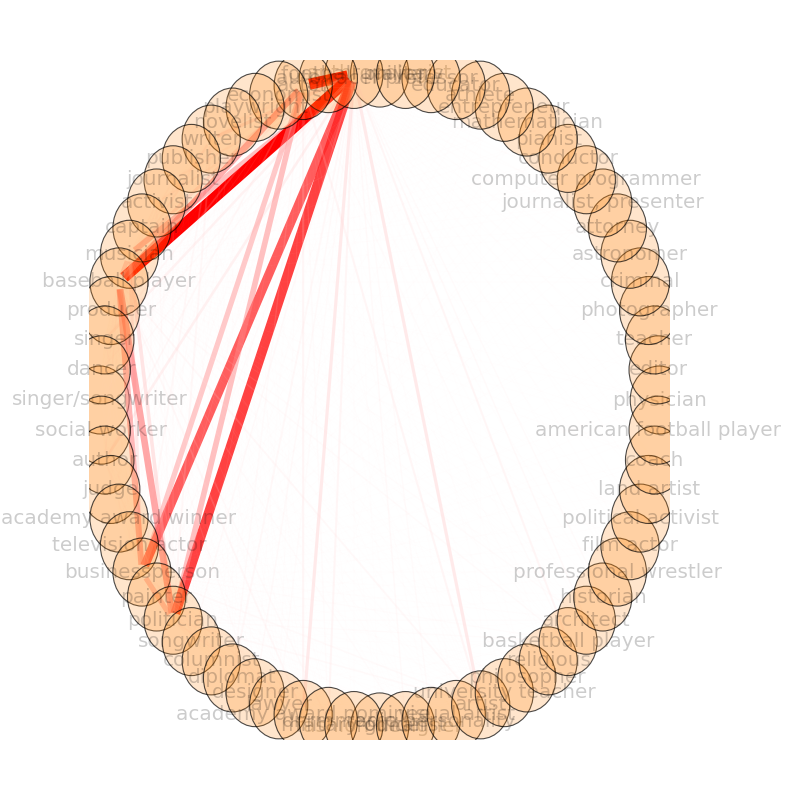

```mathematica
(* Adjust just one option stored in the graph g *)
g=SetProperty[g,EdgeStyle->ModifiedEdgePropertiesX];

Gfin=Show[g,ImagePadding->{{100,100},{100,100}}]
```